```mathematica
Needs["MiningProbabilityMultiStageProofOfWork`"]
```

```mathematica
M = 2
```

1

{0.0043601,0.9623688080989592851616972647071565956651577449549610920434304201801865635691663751114321105940948733}

{0.22744,0.9623688080989592851616972647071565956651577449549610920434304201801865635691663751114321105940948733}

52.1639

2

{0.0014864,0.3716738391003167950155017781430265058598455093202884864978691446454247398717102215890053113447323531}

{0.793487,0.3716738391003167950155017781430265058598455093202884864978691446454247398717102215890053113447323531}

533.832

3

{0.0114428,0.6077192289170161809733442693472019413844704314340912303625572664624197451954142561491157291615518079}

{56.4663,0.6077192289170161809733442693472019413844704314340912303625572664624197451954142561491157291615518079}

4934.66

4

{0.0043169,0.5951539009959730699219518504987918397440836943900432942656701727231654606751023308123154156484784042}

{31.4485,0.5951539009959730699219518504987918397440836943900432942656701727231654606751023308123154156484784042}

7284.97

5

{0.0048996,0.3804303827436575908607113095608554661252806637803910089236914448721033577961532863216770238571500022}

{5.66084,0.3804303827436575908607113095608554661252806637803910089236914448721033577961532863216770238571500022}

1155.37

6

{0.0067148,0.423882296535618639454391036204539766404016590525905369902081446760393394076543479615485266241828814}

{0.343352,0.423882296535618639454391036204539766404016590525905369902081446760393394076543479615485266241828814}

51.1336

7

{0.0119815,0.5}

{1.51854,0.5}

126.74

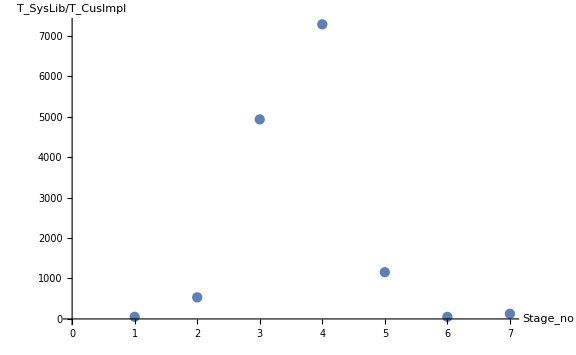

```mathematica
test = {   
{ {4},         {Pi Exp[-3]}               } ,          
  
{{5, 2/3},          { Exp[2/3], Exp[2/3]}      },

{{4^(8/9), 4^(9/10),4^(10/11)  },                   {3^(11/12), 3^(12/13), 3^(13/14)}         }, 

{{1000, Exp[ Exp[2/3]], 3/(Pi^4), 5^2  },                   {Pi/Exp[Pi],500,Pi^(4/5), 3/(Pi^4) }                  }, 

{{10000, 50000, 40000, 56666, 3000000},              {30000, 70000, 20000, 45555, 4000000}       }, 

{{7,14,21, 28, 35, 42  },                   {8,16,24,32,40,48}                 } , 

{{10 Pi,Pi 20/3, Pi 5,3 Pi , Pi 2, Pi 67  ,Pi  6},                   {Pi 3,Pi  5,Pi  10,Pi   2,Pi 67, Pi 20/3,Pi  6}                  }                  
};
resultsCustomImpl = {};
resultsSysLibr = {};
toPlot = {};
 
For[i = 1, i ≤ Length[test], i++, 

Print[i];
 ClearSystemCache[];

parameters = test[[i]];

cus =  AbsoluteTiming@ComputeMiningProbability[parameters];
AppendTo[resultsCustomImpl, cus];
Print[N[cus ,100]];
timeCustomImpl = cus[[1]];


ClearSystemCache[];
sys = AbsoluteTiming@Integrate[PDF[ HypoexponentialDistribution[parameters[[1]]] , t] * (1 - CDF[ HypoexponentialDistribution[parameters[[2]]] , t]), {t, 0, Infinity}] ;
AppendTo[resultsSysLibr, sys];
Print[N[sys ,100]];
timeSysLibr =sys[[1]];

Print[ N[timeSysLibr/timeCustomImpl, 100]];
Print[];

AppendTo[toPlot, {i, N[timeSysLibr/timeCustomImpl, 100]}];

]

list = ListPlot[toPlot, AxesLabel-> {Stage_no,T_SysLib/T_CusImpl }, LabelStyle->Larger, ImageSize->Large]
Export["twoMiners.png",list];
```

```mathematica
M = 3
```

3

1

{0.0006685,0.2666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667}

{0.0374807,0.2666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667}

56.0669

2

{0.0022055,0.4603026047516277394103683470418500678827565851484721094796965803672146387648985884953523389800551747}

{0.16518,0.4603026047516277394103683470418500678827565851484721094796965803672146387648985884953523389800551747}

74.8944

3

{0.0062233,0.8317792103228141181090767263743779076054802256945647282744076674170824105274436722108246568222141873}

{0.354514,0.8317792103228141181090767263743779076054802256945647282744076674170824105274436722108246568222141873}

56.9656

4

{0.0135469,0.3333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333}

{0.193836,0.3333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333}

14.3085

5

{0.0238484,0.629977601082672837515399473813797928246940312020351106934603046742777306518771427069294826601697577}

{14.6317,0.629977601082672837515399473813797928246940312020351106934603046742777306518771427069294826601697577}

613.528

6

{0.0320313,0.2465454454656958830567461229071422703815331083864006676821189817369844898239695408827752271985098556}

{5.81124,0.2465454454656958830567461229071422703815331083864006676821189817369844898239695408827752271985098556}

181.424

7

{0.0598586,0.03762265008308117361849095446791780090933130958474385657697764222490282487415589537757276564764540155}

{6.70301,0.03762265008308117361849095446791780090933130958474385657697764222490282487415589537757276564764540155}

111.981

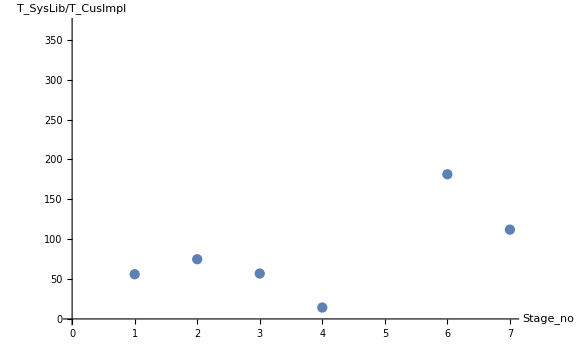

```mathematica
testM3 = {   
{ {4},        {4},              {7}          } ,   
         
{{5,40},          { 45, 3},               {4, 14}      },

{  {67, 125, 62}  ,                   {61, 53, 12},                  {2, 100, 70}  }, 

{ {35, 39, 50, 14}  ,                   {35, 39, 50, 14},                     {35, 39, 50, 14  } }, 

{ {146, 753, 134, 224, 566}  ,                   {411, 145, 225, 334, 56},                   {566, 111, 220, 100, 50  } },  

{{47, 82, 79,19,45, 89}  ,                   {62, 37, 62, 58, 56, 81},                  {55, 55, 55, 55, 55, 55  } },        

{{78, 24, 167, 456, 321, 245, 21}  ,                   {134, 135, 322, 42, 123, 245,532},                   {135, 146, 220, 532, 214,256,155  } }
};
resultsCustomImpl = {};
resultsSysLibr = {};
toPlot = {};
 
For[i = 1, i ≤ Length[testM3], i++, 

Print[i];
 ClearSystemCache[];

parameters = testM3[[i]];

cus =  AbsoluteTiming@ComputeMiningProbability[parameters];
AppendTo[resultsCustomImpl, cus];
Print[N[cus ,100]];
timeCustomImpl = cus[[1]];


ClearSystemCache[];
sys = AbsoluteTiming@Integrate[PDF[ HypoexponentialDistribution[parameters[[1]]] , t] * (1 - CDF[ HypoexponentialDistribution[parameters[[2]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[3]]] , t]), {t, 0, Infinity}] ;
AppendTo[resultsSysLibr, sys];
Print[N[sys ,100]];
timeSysLibr =sys[[1]];

Print[ N[timeSysLibr/timeCustomImpl, 100]];
Print[];

AppendTo[toPlot, {i, N[timeSysLibr/timeCustomImpl, 100]}];

]

list = ListPlot[toPlot, AxesLabel-> {Stage_no,T_SysLib/T_CusImpl }, LabelStyle->Larger, ImageSize->Large]
Export["threeMiners.png",list];
```

```mathematica
M = 4
```

1

{0.0007579,0.2352941176470588235294117647058823529411764705882352941176470588235294117647058823529411764705882353}

{0.0357834,0.2352941176470588235294117647058823529411764705882352941176470588235294117647058823529411764705882353}

47.2139

2

{0.0047435,0.4475688870542249164460582256421827428772843020397403996703246219297962626703796082521144202380327652}

{0.218015,0.4475688870542249164460582256421827428772843020397403996703246219297962626703796082521144202380327652}

45.9609

3

{0.0179693,0.4984962087357207767409872972180804441293737655372279854007913369200381328202605879678414639045368418}

{0.657293,0.4984962087357207767409872972180804441293737655372279854007913369200381328202605879678414639045368418}

36.5787

4

{0.0484952,0.3249539962958785019062789706474334904337719466913760903885698442744237644737805361227129381805956781}

{0.538144,0.3249539962958785019062789706474334904337719466913760903885698442744237644737805361227129381805956781}

11.0969

5

{0.109838,0.6140511546006955290480988317305673638683319563887105031955562808836953219640338506521049301784746746}

{17.2613,0.6140511546006955290480988317305673638683319563887105031955562808836953219640338506521049301784746746}

157.152

6

{0.20703,0.2376748797755031172863362169970110695779842615499482431583097745443126322168362483461629068537521594}

{23.7886,0.2376748797755031172863362169970110695779842615499482431583097745443126322168362483461629068537521594}

114.904

7

{0.602309,0.02473639299333571285343073564751030984695796943974156913513455375773648703378703477396331942626786647}

{19.4365,0.02473639299333571285343073564751030984695796943974156913513455375773648703378703477396331942626786647}

32.27

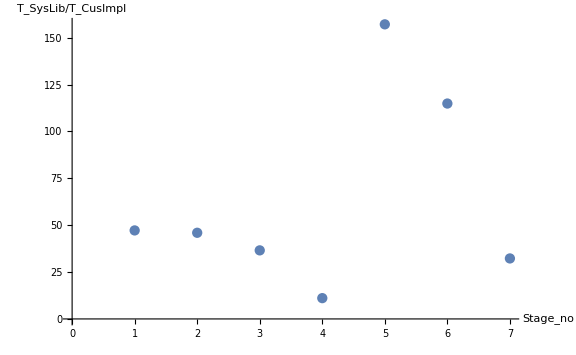

```mathematica
testM4 = {   
{ {4},        {4},       {7} ,            {2}         } ,        
    
{{5,40},          { 45, 3},    {4, 14},                  {1, 4}      },

{  {67, 125, 62}  ,                   {61, 53, 12},                {2, 100, 70},                 {56, 90, 70}  }, 

{{35, 39, 50, 14}  ,                   {35, 39, 50, 14},                   {35, 39, 50, 14  },                {25, 57, 45, 1  } }, 

{{146, 753, 134, 224, 566}  ,                   {411, 145, 225, 334, 56},               {566, 111, 220, 100, 50  },                      {32, 56, 164, 156, 94}   }, 

      {{47, 82, 79,19,45, 89}  ,                   {62, 37, 62, 58, 56, 81},                 {55, 55, 55, 55, 55, 55  }  ,                   {34,56,9,35,67,21}   },       
 
{{78, 24, 167, 456, 321, 245, 21}  ,                       {134, 135, 322, 42, 123, 245,532},                   {135, 146, 220, 532, 214,256,155  } ,                   {63, 142, 135, 324, 256,256,237  }}
};
resultsCustomImpl = {};
resultsSysLibr = {};
toPlot = {};
 
For[i = 1, i ≤ Length[testM4], i++, 

Print[i];
 ClearSystemCache[];

parameters = testM4[[i]];

cus =  AbsoluteTiming@ComputeMiningProbability[parameters];
AppendTo[resultsCustomImpl, cus];
Print[N[cus ,100]];
timeCustomImpl = cus[[1]];


ClearSystemCache[];
sys = AbsoluteTiming@Integrate[PDF[ HypoexponentialDistribution[parameters[[1]]] , t] * (1 - CDF[ HypoexponentialDistribution[parameters[[2]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[3]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[4]]] , t]), {t, 0, Infinity}] ;
AppendTo[resultsSysLibr, sys];
Print[N[sys ,100]];
timeSysLibr =sys[[1]];

Print[ N[timeSysLibr/timeCustomImpl, 100]];
Print[];

AppendTo[toPlot, {i, N[timeSysLibr/timeCustomImpl, 100]}];

]

list = ListPlot[toPlot, AxesLabel-> {Stage_no,T_SysLib/T_CusImpl }, LabelStyle->Larger, ImageSize->Large]
Export["fourMiners.png",list];
```

```mathematica
M=5
```

1

{0.0010092,0.1739130434782608695652173913043478260869565217391304347826086956521739130434782608695652173913043478}

{0.0360302,0.1739130434782608695652173913043478260869565217391304347826086956521739130434782608695652173913043478}

35.7017

2

{0.0093828,0.4155822889051830241336198418920566463737756994631638869438973958416978806857985694239496984286570369}

{0.311086,0.4155822889051830241336198418920566463737756994631638869438973958416978806857985694239496984286570369}

33.155

3

{0.0504775,0.4251819307554893422524652127768492682469639223300565967122988711682527857779132233066992645511420409}

{1.17287,0.4251819307554893422524652127768492682469639223300565967122988711682527857779132233066992645511420409}

23.2355

4

{0.17279,0.2722936379743744139396180347149415192405111684675473466654056359457683793202727909642131333172219138}

{0.896528,0.2722936379743744139396180347149415192405111684675473466654056359457683793202727909642131333172219138}

5.18854

5

{0.516474,0.4465987660726146315898824193728746967662533454439569251146929042144614592691593518864391690411919433}

{21.6938,0.4465987660726146315898824193728746967662533454439569251146929042144614592691593518864391690411919433}

42.0036

6

{1.34866,0.1780640243783150262572733067005001653056574659983146003951086343439913849084631098207143234746523133}

{42.6996,0.1780640243783150262572733067005001653056574659983146003951086343439913849084631098207143234746523133}

31.6607

7

{4.3255,0.01831404633497975921440906872605477651939761989634578601983684361844608748678983023824688790506378474}

{56.1133,0.01831404633497975921440906872605477651939761989634578601983684361844608748678983023824688790506378474}

12.9727

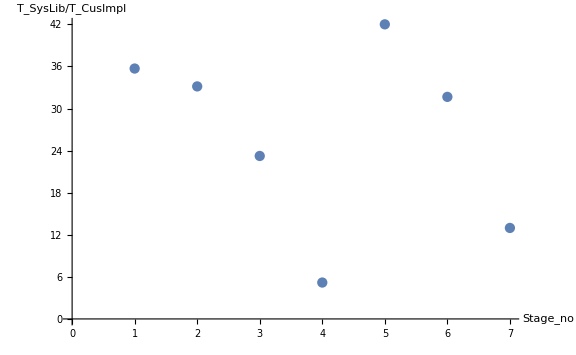

```mathematica
testM5= {   
{ {4},        {4},       {7} ,            {2} ,        {6}        } ,            

{{5,40},          { 45, 3},    {4, 14},                  {1, 4} ,           {2,7}     },

{  {67, 125, 62}  ,                   {61, 53, 12},                {2, 100, 70},                 {56, 90, 70},           {43, 47, 51}  }, 

{{35, 39, 50, 14}  ,                   {35, 39, 50, 14},                   {35, 39, 50, 14  },                {25, 57, 45, 1  } ,           {53, 12, 42, 17}}, 

{{146, 753, 134, 224, 566}  ,                   {411, 145, 225, 334, 56},               {566, 111, 220, 100, 50  },                      {32, 56, 164, 156, 94},              {266, 136, 356, 245, 134}   }, 

      {{47, 82, 79,19,45, 89}  ,                   {62, 37, 62, 58, 56, 81},                 {55, 55, 55, 55, 55, 55  }  ,                   {34,56,9,35,67,21},              {64,44, 56, 63, 45, 65}      },        

{{78, 24, 167, 456, 321, 245, 21}  ,                       {134, 135, 322, 42, 123, 245,532},                   {135, 146, 220, 532, 214,256,155  } ,                   {63, 142, 135, 324, 256,256,237  },       {123, 245, 143, 156, 163, 167, 167}}
};
resultsCustomImpl = {};
resultsSysLibr = {};
toPlot = {};
 
For[i = 1, i ≤ Length[testM5], i++, 

Print[i];
 ClearSystemCache[];

parameters = testM5[[i]];

cus =  AbsoluteTiming@ComputeMiningProbability[parameters];
AppendTo[resultsCustomImpl, cus];
Print[N[cus ,100]];
timeCustomImpl = cus[[1]];


ClearSystemCache[];
sys = AbsoluteTiming@Integrate[PDF[ HypoexponentialDistribution[parameters[[1]]] , t] * (1 - CDF[ HypoexponentialDistribution[parameters[[2]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[3]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[4]]] , t])  * (1 - CDF[ HypoexponentialDistribution[parameters[[5]]] , t]), {t, 0, Infinity}] ;
AppendTo[resultsSysLibr, sys];
Print[N[sys ,100]];
timeSysLibr =sys[[1]];

Print[ N[timeSysLibr/timeCustomImpl, 100]];
Print[];

AppendTo[toPlot, {i, N[timeSysLibr/timeCustomImpl, 100]}];

]

list = ListPlot[toPlot, AxesLabel-> {Stage_no,T_SysLib/T_CusImpl }, LabelStyle->Larger, ImageSize->Large]
Export["fiveMiners.png",list];
```

```mathematica
M = 10
```

1

{0.0018614,0.06349206349206349206349206349206349206349206349206349206349206349206349206349206349206349206349206349}

{0.0360708,0.06349206349206349206349206349206349206349206349206349206349206349206349206349206349206349206349206349}

19.3783

2

{0.264226,0.1687763338182290803586116466355243559337736336675867156684367598783647913676035983433281683864338703}

{0.869326,0.1687763338182290803586116466355243559337736336675867156684367598783647913676035983433281683864338703}

3.29009

3

{11.7225,0.411871374478188827699837390848903462936666175182291675362240548610717302332283358416035949973233412}

{2.47971,0.411871374478188827699837390848903462936666175182291675362240548610717302332283358416035949973233412}

0.211535

4

{250.641,0.2300211241949999571621079508029159072636367492728351132886978586696827933863837350524654626506333176}

{32.8743,0.2300211241949999571621079508029159072636367492728351132886978586696827933863837350524654626506333176}

0.131161

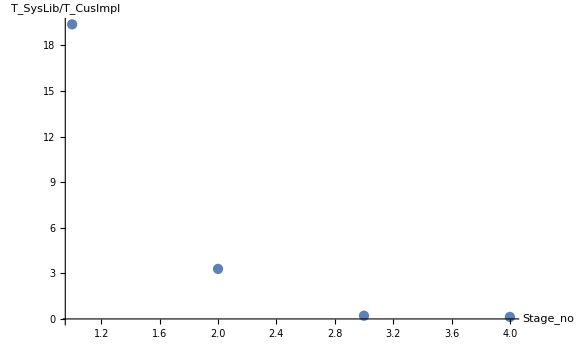

```mathematica
testM10= {   
{ {4},        {4},       {7} ,            {2} ,        {6}   ,  {6}  ,  {7} ,  {8} ,  {9} ,  {10} } ,            

{{5,40},          { 45, 3},    {4, 14},                  {1, 4} ,           {2,7},           {6,7} ,           {7,13} ,           {8,14} ,           {9,14} ,           {10,11} },

{  {67, 125, 62}  ,                   {61, 53, 12},                {2, 100, 70},                 {56, 90, 70},           {43, 47, 51},   {6,7, 54} ,           {7,13, 23} ,           {8,14,23} ,           {9,14,31} ,           {10,11,12} },


{{35, 39, 50, 14}  ,                   {35, 39, 50, 14},                   {35, 39, 50, 14  },                {25, 57, 45, 1  } ,           {53, 12, 42, 17},     {6,7, 54, 34} ,           {7,13, 23,13} ,           {8,14,23,34} ,           {9,14,31,14} ,           {10,11,12,12}}
};
resultsCustomImpl = {};
resultsSysLibr = {};
toPlot = {};
 
For[i = 1, i ≤ Length[testM10], i++, 

Print[i];
 ClearSystemCache[];

parameters = testM10[[i]];

cus =  AbsoluteTiming@ComputeMiningProbability[parameters];
AppendTo[resultsCustomImpl, cus];
Print[N[cus ,100]];
timeCustomImpl = cus[[1]];


ClearSystemCache[];
sys = AbsoluteTiming@Integrate[PDF[ HypoexponentialDistribution[parameters[[1]]] , t] * (1 - CDF[ HypoexponentialDistribution[parameters[[2]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[3]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[4]]] , t])  * (1 - CDF[ HypoexponentialDistribution[parameters[[5]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[6]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[7]]] , t])  * (1 - CDF[ HypoexponentialDistribution[parameters[[8]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[9]]] , t]) * (1 - CDF[ HypoexponentialDistribution[parameters[[10]]] , t]) , {t, 0, Infinity}] ;
AppendTo[resultsSysLibr, sys];
Print[N[sys ,100]];
timeSysLibr =sys[[1]];

Print[ N[timeSysLibr/timeCustomImpl, 100]];
Print[];

AppendTo[toPlot, {i, N[timeSysLibr/timeCustomImpl, 100]}];

]

list = ListPlot[toPlot, AxesLabel-> {Stage_no,T_SysLib/T_CusImpl }, LabelStyle->Larger, ImageSize->Large]
```